```mathematica
ClearAll["Global`*"]
```

```mathematica
F1 [x_, y_,a_, b_] := a-(b+1)x+x^2y
```

```mathematica
F2[x_, y_,a_, b_] := b x -x^2 y
```

```mathematica
F1[x,y,a,b]
```

a-(b+1) x+x^2 y

```mathematica
F2[x,y,a,b]
```

b x-x^2 y

```mathematica
Reduce[{0 == F1[x,y,a,b], 0 == F2[x,y,a,b], a>0,b>0}, { x,y}]
```

b>0∧a>0∧x==a∧y==b/x

```mathematica
J=Simplify[D[{F1[x,y,a,b], F2[x,y,a,b]},{{ x,y}}]]
```

(-b+2 x y-1 | x^2
b-2 x y | -x^2)

```mathematica
TeXForm[J]
```

\left(
\begin{array}{cc}
 -b+2 x y-1 & x^2 \\
 b-2 x y & -x^2 \\
\end{array}
\right)

```mathematica
Simplify[Eigenvalues[J]]
```

{1/2 (-√((b+x^2-2 x y+1)^2-4 x^2)-b-x^2+2 x y-1),1/2 (√((b+x^2-2 x y+1)^2-4 x^2)-b-x^2+2 x y-1)}

```mathematica
x=a ;y=b/x
```

b/a

```mathematica
J
```

(b-1 | a^2
-b | -a^2)

```mathematica
TeXForm[J]
```

\left(
\begin{array}{cc}
 b-1 & a^2 \\
 -b & -a^2 \\
\end{array}
\right)

```mathematica
Simplify[Eigenvalues[J]]
```

{1/2 (-√((a^2-b+1)^2-4 a^2)-a^2+b-1),1/2 (√((a^2-b+1)^2-4 a^2)-a^2+b-1)}

```mathematica
TeXForm[Simplify[Eigenvalues[J]]]
```

\left\{\frac{1}{2} \left(-\sqrt{\left(a^2-b+1\right)^2-4 a^2}-a^2+b-1\right),\frac{1}{2} \left(\sqrt{\left(a^2-b+1\right)^2-4
   a^2}-a^2+b-1\right)\right\}

```mathematica
Reduce[{1/2 (√((a^2-b+1)^2-4 a^2)-a^2+b-1)>0,1/2 (-√((a^2-b+1)^2-4 a^2)-a^2+b-1)>0 ,a>0,b>0}, { a}]
```

b>1∧0<a≤√b-1

```mathematica
Reduce[{1/2 (√((a^2-b+1)^2-4 a^2)-a^2+b-1)<0,1/2 (-√((a^2-b+1)^2-4 a^2)-a^2+b-1)<0, a>0,b>0}, { a}]
```

(0<b≤1∧(0<a≤1-√b∨a≥√b+1))∨(b>1∧a≥√b+1)

```mathematica
Plot3D[1/2 (√((a^2-b+1)^2-4 a^2)-a^2+b-1),{a,0,4},{b,0,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[1/2 (-√((a^2-b+1)^2-4 a^2)-a^2+b-1),{a,0,4},{b,0,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Reduce[{1/2 (√((a^2-b+1)^2-4 a^2)-a^2+b-1)>0,1/2 (-√((a^2-b+1)^2-4 a^2)-a^2+b-1)>0 ,a>0,b>0}, { a}]
```

b>1∧0<a≤√b-1

```mathematica
Reduce[{Re[1/2 (-√((a^2-b+1)^2-4 a^2)-a^2+b-1)]>0,Re[1/2 (√((a^2-b+1)^2-4 a^2)-a^2+b-1)]>0 ,a>0,b>0}, { a}]
```

b>1∧(√b-1≤a<√(b-1)∨0<a<√b-1)

```mathematica
Reduce[{1/2 (√((a^2-b+1)^2-4 a^2)-a^2+b-1)<0,1/2 (-√((a^2-b+1)^2-4 a^2)-a^2+b-1)<0, a>0,b>0}, { a}]
```

(0<b≤1∧(0<a≤1-√b∨a≥√b+1))∨(b>1∧a≥√b+1)

```mathematica
Reduce[{(a^2-b+1)^2-4 a^2<0, a>0,b>0}, { a}]
```

(0<b≤1∧1-√b<a<√b+1)∨(b>1∧√b-1<a<√b+1)

```mathematica
Reduce[{Re[1/2 (-√((a^2-b+1)^2-4 a^2)-a^2+b-1)]<0,Re[1/2 (√((a^2-b+1)^2-4 a^2)-a^2+b-1)]<0, a>0,b>0}, { a}]
```

(0<b<1∧1-√b≤a≤√b+1)∨(b≥1∧√(b-1)<a≤√b+1)∨(0<b≤1∧(0<a<1-√b∨a>√b+1))∨(b>1∧a>√b+1)

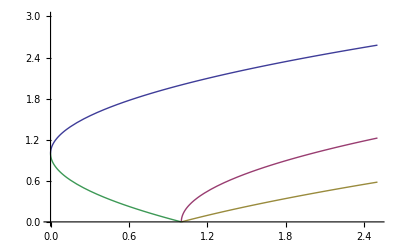

```mathematica
Plot[{1 + Sqrt[b], Sqrt[-1 + b], Sqrt[ b]-1, 1 - Sqrt[b]}, {b,0, 2.5},PlotRange->{0,3}]
```

```mathematica
Plot3D[Re[1/2 (-√((a^2-b+1)^2-4 a^2)-a^2+b-1)],{a,0,4},{b,0,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Re[1/2 (√((a^2-b+1)^2-4 a^2)-a^2+b-1)],{a,0,4},{b,0,10},AxesLabel->Automatic]
```

-Graphics3D-